## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="FBA1";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;

(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/MASSef/";
kineticDataFileName =  "kinetic_data_MASSef.csv";

mainFolder = "fit_FBA1";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/MASSef/examples/FBA1/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{fdp,Null,Keq substrate}

{0.00016,Keq value}

{fdp,Km or S05 substrate}

{0.00002,Km or S05 value}

{{{fdp,Null}},kcat substrates}

{0.217,kcat value}

{fdp,Km or S05 substrate}

{0.00002,Km or S05 value}

{{{fdp,Null},{cit,0.011}},kcat substrates}

{3.17,kcat value}

{fdp,Km or S05 substrate}

{0.00007,Km or S05 value}

(fdp^c⇌dhap^c+g3p^c)^FBA1

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 8-10

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 0.00016 | 0.000152
0.000168 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00002 | 0.000019
0.000021 |  | M | 7.5 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00002 | 0.000018
0.000022 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00007 | 0.000058
0.000082 | cit | 0.011 | M | 8 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 0.412114 | 0.39882
0.423509 | 1/s | 8 | 37 | trishcl | 0.05 | 
1 | fdp | Null
cit | 0.011 | 6.02029 | 5.71642
6.32415 | 1/s | 8 | 37 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {0,10,10};
s05Priorities = Null;
kcatPriorities = {2,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c⇌dhap^c+g3p^c)^FBA1

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 8-10

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 0.00016 | 0.000152
0.000168 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
10 | fdp | 0.00002 | 0.000018
0.000022 |  | M | 8 | 30 | trishcl | 0.05 | 
10 | fdp | 0.00007 | 0.000058
0.000082 | cit | 0.011 | M | 8 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
2 | fdp | Null | 0.412114 | 0.39882
0.423509 | 1/s | 8 | 37 | trishcl | 0.05 | 
1 | fdp | Null
cit | 0.011 | 6.02029 | 5.71642
6.32415 | 1/s | 8 | 37 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Construct Module and Set Up Comparison Equations

```mathematica
haldaneRatiosList
```

{(k_FBA12^⟶ k_FBA14^⟶ k_FBA15^⟶ k_FBA18^⟶)/(k_FBA12^⟵ k_FBA14^⟵ k_FBA15^⟵ k_FBA18^⟵),(k_FBA13^⟶ k_FBA16^⟶ k_FBA17^⟶ k_FBA19^⟶)/(k_FBA13^⟵ k_FBA16^⟵ k_FBA17^⟵ k_FBA19^⟵)}

### Construct enzyme module

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

```mathematica
catalyticBranch={"E_FBA1[c] + fdp[c] <=> E_FBA1[c]&fdp",
				"E_FBA1[c]&fdp <=> E_FBA1[c]&dhap&g3p",
				"E_FBA1[c]&dhap&g3p <=> E_FBA1[c]&dhap + g3p[c]",
				"E_FBA1[c]&dhap <=> E_FBA1[c] + dhap[c]",
				
				"E_FBA1[c] + cit[c] <=> E_FBA1[c]&cit",
				"E_FBA1[c]&cit + fdp[c] <=> E_FBA1[c]&cit&fdp",
				"E_FBA1[c]&cit&fdp <=> E_FBA1[c]&cit&dhap&g3p",
				"E_FBA1[c]&cit&dhap&g3p <=> E_FBA1[c]&cit&dhap + g3p[c]",
				"E_FBA1[c]&cit&dhap <=> E_FBA1[c]&cit + dhap[c]"};


enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((FBA1^c)_^+cit^c⇌(FBA1^c&cit^c)_^)^FBA11,((FBA1^c)_^+fdp^c⇌(FBA1^c&fdp^c)_^)^FBA12,((FBA1^c&cit^c)_^+fdp^c⇌(FBA1^c&cit^c&fdp^c)_^)^FBA13,((FBA1^c&dhap^c)_^⇌(FBA1^c)_^+dhap^c)^FBA14,((FBA1^c&fdp^c)_^⇌(FBA1^c&dhap^c&g3p^c)_^)^FBA15,((FBA1^c&cit^c&dhap^c)_^⇌(FBA1^c&cit^c)_^+dhap^c)^FBA16,((FBA1^c&cit^c&fdp^c)_^⇌(FBA1^c&cit^c&dhap^c&g3p^c)_^)^FBA17,((FBA1^c&dhap^c&g3p^c)_^⇌(FBA1^c&dhap^c)_^+g3p^c)^FBA18,((FBA1^c&cit^c&dhap^c&g3p^c)_^⇌(FBA1^c&cit^c&dhap^c)_^+g3p^c)^FBA19}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((FBA1^c)_^+fdp^c⇌(FBA1^c&fdp^c)_^)^FBA12,Overscript[(FBA1^c&dhap^c)_^⇌(FBA1^c)_^+dhap^c, FBA14],((FBA1^c&fdp^c)_^⇌(FBA1^c&dhap^c&g3p^c)_^)^FBA15,Overscript[(FBA1^c&dhap^c&g3p^c)_^⇌(FBA1^c&dhap^c)_^+g3p^c, FBA18]};
catalyticReactionsSet2={((FBA1^c&cit^c)_^+fdp^c⇌(FBA1^c&cit^c&fdp^c)_^)^FBA13,Overscript[(FBA1^c&cit^c&dhap^c)_^⇌(FBA1^c&cit^c)_^+dhap^c, FBA16],((FBA1^c&cit^c&fdp^c)_^⇌(FBA1^c&cit^c&dhap^c&g3p^c)_^)^FBA17,Overscript[(FBA1^c&cit^c&dhap^c&g3p^c)_^⇌(FBA1^c&cit^c&dhap^c)_^+g3p^c, FBA19]};
catalyticReactionsSetsList = {catalyticReactionsSet1, catalyticReactionsSet2};
```

```mathematica
catalyticReactionsSet1={((FBA1^c)_^+fdp^c⇌(FBA1^c&fdp^c)_^)^FBA11,Overscript[(FBA1^c&dhap^c)_^⇌(FBA1^c)_^+dhap^c, FBA12],((FBA1^c&fdp^c)_^⇌(FBA1^c&dhap^c&g3p^c)_^)^FBA13,Overscript[(FBA1^c&dhap^c&g3p^c)_^⇌(FBA1^c&dhap^c)_^+g3p^c, FBA14]};
catalyticReactionsSet2={Overscript[(FBA1^c)_^(cit^c)+fdp^c⇌(FBA1^c&fdp^c)_^(cit^c), FBA11$3],Overscript[(FBA1^c&dhap^c)_^(cit^c)⇌(FBA1^c)_^(cit^c)+dhap^c, FBA12$3],Overscript[(FBA1^c&fdp^c)_^(cit^c)⇌(FBA1^c&dhap^c&g3p^c)_^(cit^c), FBA13$3],Overscript[(FBA1^c&dhap^c&g3p^c)_^(cit^c)⇌(FBA1^c&dhap^c)_^(cit^c)+g3p^c, FBA14$3]};
catalyticReactionsSetsList = {enzymeModelOrig["Reactions"]};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{fdp^c→0}

{dhap^c→0,g3p^c→0}

{fdp^c→∞}

{dhap^c→∞,g3p^c→∞}

Added inhibition reactions:

{}

Loading flux equation...

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Loading relative rate reverse equation...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

Elementary reactions

{((FBA1^c)_^+cit^c⇌(FBA1^c&cit^c)_^)^FBA11,((FBA1^c)_^+fdp^c⇌(FBA1^c&fdp^c)_^)^FBA12,((FBA1^c&cit^c)_^+fdp^c⇌(FBA1^c&cit^c&fdp^c)_^)^FBA13,((FBA1^c&dhap^c)_^⇌(FBA1^c)_^+dhap^c)^FBA14,((FBA1^c&fdp^c)_^⇌(FBA1^c&dhap^c&g3p^c)_^)^FBA15,((FBA1^c&cit^c&dhap^c)_^⇌(FBA1^c&cit^c)_^+dhap^c)^FBA16,((FBA1^c&cit^c&fdp^c)_^⇌(FBA1^c&cit^c&dhap^c&g3p^c)_^)^FBA17,((FBA1^c&dhap^c&g3p^c)_^⇌(FBA1^c&dhap^c)_^+g3p^c)^FBA18,((FBA1^c&cit^c&dhap^c&g3p^c)_^⇌(FBA1^c&cit^c&dhap^c)_^+g3p^c)^FBA19}

Equation used to fit the forward kcat

(fdp^c FBA1_total_Global k_FBA14^⟶ k_FBA16^⟶ (cit^c k_FBA11^⟶ k_FBA13^⟶ k_FBA17^⟶ (k_FBA15^⟶ k_FBA18^⟶+k_FBA12^⟵ (k_FBA15^⟵+k_FBA18^⟶)) k_FBA19^⟶+k_FBA11^⟵ k_FBA12^⟶ k_FBA15^⟶ k_FBA18^⟶ (k_FBA17^⟶ k_FBA19^⟶+k_FBA13^⟵ (k_FBA17^⟵+k_FBA19^⟶))))/(k_FBA11^⟵ k_FBA16^⟶ (k_FBA14^⟶ k_FBA15^⟶ k_FBA18^⟶+k_FBA12^⟵ k_FBA14^⟶ (k_FBA15^⟵+k_FBA18^⟶)+fdp^c k_FBA12^⟶ (k_FBA15^⟶ k_FBA18^⟶+k_FBA14^⟶ (k_FBA15^⟵+k_FBA15^⟶+k_FBA18^⟶))) (k_FBA17^⟶ k_FBA19^⟶+k_FBA13^⟵ (k_FBA17^⟵+k_FBA19^⟶))+cit^c k_FBA11^⟶ k_FBA14^⟶ (k_FBA15^⟶ k_FBA18^⟶+k_FBA12^⟵ (k_FBA15^⟵+k_FBA18^⟶)) (k_FBA16^⟶ k_FBA17^⟶ k_FBA19^⟶+k_FBA13^⟵ k_FBA16^⟶ (k_FBA17^⟵+k_FBA19^⟶)+fdp^c k_FBA13^⟶ (k_FBA17^⟶ k_FBA19^⟶+k_FBA16^⟶ (k_FBA17^⟵+k_FBA17^⟶+k_FBA19^⟶))))

r

```mathematica
relativeRateForward[[1]]
```

(fdp^c (k_FBA11^⟵ k_FBA12^⟶ k_FBA16^⟶ (k_FBA15^⟶ k_FBA18^⟶+k_FBA14^⟶ (k_FBA15^⟵+k_FBA15^⟶+k_FBA18^⟶)) (k_FBA17^⟶ k_FBA19^⟶+k_FBA13^⟵ (k_FBA17^⟵+k_FBA19^⟶))+cit^c k_FBA11^⟶ k_FBA13^⟶ k_FBA14^⟶ (k_FBA15^⟶ k_FBA18^⟶+k_FBA12^⟵ (k_FBA15^⟵+k_FBA18^⟶)) (k_FBA17^⟶ k_FBA19^⟶+k_FBA16^⟶ (k_FBA17^⟵+k_FBA17^⟶+k_FBA19^⟶))))/(k_FBA11^⟵ k_FBA16^⟶ (k_FBA14^⟶ k_FBA15^⟶ k_FBA18^⟶+k_FBA12^⟵ k_FBA14^⟶ (k_FBA15^⟵+k_FBA18^⟶)+fdp^c k_FBA12^⟶ (k_FBA15^⟶ k_FBA18^⟶+k_FBA14^⟶ (k_FBA15^⟵+k_FBA15^⟶+k_FBA18^⟶))) (k_FBA17^⟶ k_FBA19^⟶+k_FBA13^⟵ (k_FBA17^⟵+k_FBA19^⟶))+cit^c k_FBA11^⟶ k_FBA14^⟶ (k_FBA15^⟶ k_FBA18^⟶+k_FBA12^⟵ (k_FBA15^⟵+k_FBA18^⟶)) (k_FBA16^⟶ k_FBA17^⟶ k_FBA19^⟶+k_FBA13^⟵ k_FBA16^⟶ (k_FBA17^⟵+k_FBA19^⟶)+fdp^c k_FBA13^⟶ (k_FBA17^⟶ k_FBA19^⟶+k_FBA16^⟶ (k_FBA17^⟵+k_FBA17^⟶+k_FBA19^⟶))))

```mathematica
FBA1RateConsts=finalRateConsts
Export[inputPath<>"/"<>rxnName<>"_rateConsts.m",FBA1RateConsts, "MX"]
```

{k_FBA11^⟵,k_FBA11^⟶,k_FBA12^⟵,k_FBA12^⟶,k_FBA13^⟵,k_FBA13^⟶,k_FBA14^⟵,k_FBA14^⟶}

/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBA1/fit_FBA1/input/FBA1_rateConsts.m

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	fdp[c]	g3p[c]	cit[c]	param_FBA1_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
1	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/haldaneRatio_2.txt"	0.00016
10	0	2.0000000000000003e-6	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.09090909090909091
10	0	3.1697863849222286e-6	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.13680688860321005
10	0	5.023772863019165e-6	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.20076000891310186
10	0	7.96214341106994e-6	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.2847472489508013
10	0	0.000012619146889603861	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.3868631798468569
10	0	0.00002	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.49999999999999994
10	0	0.00003169786384922229	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.6131368201531432
10	0	0.00005023772863019165	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.7152527510491988
10	0	0.00007962143411069939	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.7992399910868981
10	0	0.0001261914688960386	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.86319311139679
10	0	0.00020000000000000004	0	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.9090909090909092
10	0	7.000000000000002e-6	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.09090909090909094
10	0	0.000011094252347227801	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.13680688860321008
10	0	0.00001758320502056708	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.20076000891310194
10	0	0.000027867501938744792	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.2847472489508013
10	0	0.000044167014113613516	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.3868631798468569
10	0	0.00007000000000000002	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.5000000000000001
10	0	0.00011094252347227801	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.6131368201531432
10	0	0.0001758320502056708	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.7152527510491989
10	0	0.0002786750193874482	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.7992399910868984
10	0	0.0004416701411361352	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.86319311139679
10	0	0.0007000000000000001	0	0.011	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/relRateFor_fdp.txt"	0.9090909090909092
2	0	0.01	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
2	0	0.01	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
2	0	0.01	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
2	0	0.01	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
2	0	0.01	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
2	0	0.01	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
2	0	0.01	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
2	0	0.01	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
2	0	0.01	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
2	0	0.01	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
2	0	0.01	0	0	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	0.41211435266581287
1	0	0.01	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	0.01	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	0.01	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	0.01	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	0.01	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	0.01	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	0.01	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	0.01	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	0.01	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	0.01	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064
1	0	0.01	0	0.011	1	8	37	"/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/input/absRateFor.txt"	6.020288008989064

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=1200;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];

{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 12.0297520665
best_fit: 11.9797328143
best_fit: 11.9873004161
best_fit: 11.9798952473
best_fit: 11.9846542892
best_fit: 11.9960516389
best_fit: 11.9797201078
best_fit: 61.4553581743
best_fit: 11.979844206
best_fit: 11.9798270099
best_fit: 62.849229228
best_fit: 11.9812317407
best_fit: 11.979706452
best_fit: 62.8506355067
best_fit: 11.9848205562
best_fit: 62.8492195255
best_fit: 11.9842698451
best_fit: 62.8492286083
best_fit: 12.0123997647
best_fit: 62.8497087215
best_fit: 62.8643630819
best_fit: 62.8515558998
best_fit: 12.1938008489
best_fit: 62.8489904607
best_fit: 11.9810056971
best_fit: 11.9807103305
best_fit: 12.0706988012
best_fit: 11.9797274981
best_fit: 62.016900589
best_fit: 11.9796682599
best_fit: 12.0311477056
best_fit: 11.9809722238
best_fit: 11.9804159594
best_fit: 11.9826462801
best_fit: 62.8492410289
best_fit: 43.1666384946
best_fit: 11.984929299
best_fit: 12.000283094
best_fit: 62.8527776584
best_fit: 62.0538451562
best_fit: 62.8492275721
best_fit: 11.9806655642
best_fit: 12.1331631012
best_fit: 11.9815415656
best_fit: 12.044883783
best_fit: 11.9800596242
best_fit: 11.9799514907
best_fit: 12.132394949
best_fit: 62.8492457327
best_fit: 62.8493783428
best_fit: 11.9797065865
best_fit: 11.9800657053
best_fit: 12.1528564407
best_fit: 11.985501324
best_fit: 11.9904224961
best_fit: 11.9878280824
best_fit: 12.0646893101
best_fit: 62.8492366618
best_fit: 11.9809006077
best_fit: 62.8493115896
best_fit: 12.0134418337
best_fit: 11.9908890077
best_fit: 62.8496056055
best_fit: 11.9797063005
best_fit: 62.8512911578
best_fit: 62.8492319567
best_fit: 12.1734598209
best_fit: 12.0152617081
best_fit: 11.9868414341
best_fit: 12.0914148129
best_fit: 11.9803193839
best_fit: 4.95378172614
best_fit: 13.5824666281
best_fit: 12.1190844336
best_fit: 62.8493904877
best_fit: 62.0189612193
best_fit: 11.981997795
best_fit: 11.9867257606
best_fit: 62.8494149741
best_fit: 62.0172655804
best_fit: 62.8492720281
best_fit: 62.3935762126
best_fit: 12.1588176738
best_fit: 11.9911666285
best_fit: 11.9901780304
best_fit: 51.0706634386
best_fit: 11.9862415189
best_fit: 11.9802128067
best_fit: 61.9922786516
best_fit: 11.9797675701
best_fit: 11.9899120029
best_fit: 11.9828579118
best_fit: 11.9875645014
best_fit: 12.0956511832
best_fit: 62.8492277343
best_fit: 11.9808465325
best_fit: 11.9858334823
best_fit: 62.87496069
best_fit: 62.8492271347
best_fit: 62.8919006814
best_fit: 11.9970394877
best_fit: 62.0221748516
best_fit: 12.0107893678
best_fit: 11.9958936642
best_fit: 12.1107703463
best_fit: 11.9803529756
best_fit: 11.9910473857
best_fit: 20.5369084357
best_fit: 11.9814486178
best_fit: 11.9803295303
best_fit: 13.7956782985
best_fit: 62.8494251871
best_fit: 12.0153942014
best_fit: 12.0179362367
best_fit: 11.9873670753
best_fit: 12.001422694
best_fit: 11.9799464891
best_fit: 11.9797949223
best_fit: 12.2325195597
best_fit: 12.0017526515
best_fit: 62.849261721
best_fit: 11.9800702803
best_fit: 11.9797672669
best_fit: 11.9797056337
best_fit: 12.0099178433
best_fit: 11.9906866229
best_fit: 11.9882138763
best_fit: 62.8499912599
best_fit: 11.9792087928
best_fit: 11.9797190397
best_fit: 11.9814692261
best_fit: 11.9802753347
best_fit: 11.9801633951
best_fit: 11.981709697
best_fit: 11.9797275838
best_fit: 12.03935818
best_fit: 11.980931801
best_fit: 62.8496672087
best_fit: 62.8492341745
best_fit: 11.9972805343
best_fit: 11.9821055908
best_fit: 62.8490692453
best_fit: 11.9797184978
best_fit: 62.8492297434
best_fit: 11.9799162023
best_fit: 11.9801829063
best_fit: 11.9799176537
best_fit: 11.9797329503
best_fit: 11.9803436079
best_fit: 62.8492339518
best_fit: 12.0630767027
best_fit: 11.9872646613
best_fit: 11.9797338527
best_fit: 12.0258818588
best_fit: 12.0033701383
best_fit: 62.8500233041
best_fit: 52.695969326
best_fit: 11.9798772598
best_fit: 11.9835915472
best_fit: 62.8493041305
best_fit: 11.9797546907
best_fit: 11.9843361076
best_fit: 11.9881993853
best_fit: 11.9812575418
best_fit: 62.8494136166
best_fit: 62.8492330563
best_fit: 62.849440335
best_fit: 11.9797129805
best_fit: 62.8492384393
best_fit: 11.9801585796
best_fit: 11.9833567438
best_fit: 11.983419395
best_fit: 11.980410411
best_fit: 11.9797173803
best_fit: 62.8492271668
best_fit: 62.8492307283
best_fit: 11.9912682668
best_fit: 11.9797633152
best_fit: 61.9980538926
best_fit: 1.0347025769
best_fit: 12.2914154536
best_fit: 62.8492292585
best_fit: 11.9990553222
best_fit: 11.9918105215
best_fit: 11.5148310104
best_fit: 11.9967496304
best_fit: 62.8492835702
best_fit: 11.9799080624
best_fit: 11.980530499
best_fit: 11.9798974052
best_fit: 62.8494870326
best_fit: 11.9812244199
best_fit: 58.3840270498
best_fit: 62.8492570818
best_fit: 12.009419131
best_fit: 62.8745472716
best_fit: 62.8492276831
best_fit: 11.980756567
best_fit: 11.9819673904
best_fit: 12.2942060362
best_fit: 16.7825261301
best_fit: 12.1299043098
best_fit: 62.8573132923
best_fit: 1.1491096334
best_fit: 1.09715907682
best_fit: 11.980194177
best_fit: 11.9803575371
best_fit: 11.9800132387
best_fit: 11.9802873775
best_fit: 62.849746217
best_fit: 62.8495207731
best_fit: 11.980150912
best_fit: 11.984130983
best_fit: 62.8492635281
best_fit: 12.1516975466
best_fit: 11.9830839262
best_fit: 11.9804320901
best_fit: 62.8493192232
best_fit: 11.9801476247
best_fit: 11.979705788
best_fit: 12.0061355983
best_fit: 11.9935778203
best_fit: 11.985293556
best_fit: 12.9390612794
best_fit: 11.9899018927
best_fit: 11.9810577788
best_fit: 11.9800430794
best_fit: 11.996052691
best_fit: 11.9818080093
best_fit: 11.9810562906
best_fit: 62.0169581126
best_fit: 11.9797076421
best_fit: 11.9800279389
best_fit: 62.0170190692
best_fit: 12.0258491667
best_fit: 12.0316327593
best_fit: 12.1159635151
best_fit: 12.0463803681
best_fit: 11.979759851
best_fit: 62.8492342738
best_fit: 60.5352908848
best_fit: 11.9797620205
best_fit: 12.0257749836
best_fit: 11.9884750287
best_fit: 11.9817887498
best_fit: 11.9812010194
best_fit: 11.9799350778
best_fit: 12.2358929492
best_fit: 12.0687265344
best_fit: 11.9805233748
best_fit: 62.8492336655
best_fit: 11.9928258309
best_fit: 12.0338100945
best_fit: 12.0949269786
best_fit: 0.94258710008
best_fit: 11.9665958147
best_fit: 62.84923254
best_fit: 12.1406759341
best_fit: 58.8540827992
best_fit: 12.0165954056
best_fit: 62.8492968503
best_fit: 13.0042941245
best_fit: 11.984828755
best_fit: 62.0169004614
best_fit: 12.3122172728
best_fit: 11.9808775938
best_fit: 11.9810536063
best_fit: 11.9820436242
best_fit: 11.9797128167
best_fit: 11.9851963047
best_fit: 0.80326040055
best_fit: 12.0238602021
best_fit: 62.8500036153
best_fit: 62.8497120026
best_fit: 62.027291268
best_fit: 62.8492267353
best_fit: 11.979801001
best_fit: 62.8494794742
best_fit: 1.07892379155
best_fit: 12.0706629766
best_fit: 11.9869338589
best_fit: 12.0969561796
best_fit: 11.9799927395
best_fit: 62.8492327808
best_fit: 11.9824844074
best_fit: 62.8492276835
best_fit: 12.2346910354
best_fit: 12.0061206549
best_fit: 11.9799847828
best_fit: 11.9800683507
best_fit: 11.9836875433
best_fit: 62.8493137734
best_fit: 12.1011510377
best_fit: 11.9856866437
best_fit: 11.9877290987
best_fit: 12.3170803298
best_fit: 62.8505279975
best_fit: 11.9971984266
best_fit: 62.8521899132
best_fit: 12.4724060018
best_fit: 1.0934565508
best_fit: 12.0021416565
best_fit: 11.9887718495
best_fit: 12.2048052162
best_fit: 62.8492277068
best_fit: 62.8492571289
best_fit: 62.8492387266
best_fit: 62.2790464462
best_fit: 12.0701095758
best_fit: 12.0222955797
best_fit: 62.8469438775
best_fit: 62.8510514774
best_fit: 11.9797617445
best_fit: 62.8490488111
best_fit: 11.9814951798
best_fit: 62.8492810543
best_fit: 11.9800185897
best_fit: 12.0308899345
best_fit: 11.9880458733
best_fit: 11.9799544973
best_fit: 11.9799827077
best_fit: 11.9797785938
best_fit: 0.863153248989
best_fit: 11.9797270548
best_fit: 62.8492340766
best_fit: 11.9786870023
best_fit: 12.0030961836
best_fit: 12.1668460148
best_fit: 11.985138644
best_fit: 11.9797763982
best_fit: 62.8492276861
best_fit: 11.9799908528
best_fit: 11.9801519418
best_fit: 11.9828847232
best_fit: 62.8492277157
best_fit: 11.9891792272
best_fit: 11.9822254711
best_fit: 12.0025264261
best_fit: 62.8492306259
best_fit: 11.979834861
best_fit: 12.093213873
best_fit: 11.985222119
best_fit: 11.9797056703
best_fit: 11.9797128875
best_fit: 62.8492278517
best_fit: 1.00733737421
best_fit: 62.8492618878
best_fit: 12.0855687297
best_fit: 62.8493058595
best_fit: 11.9799545785
best_fit: 12.0003641349
best_fit: 12.195069267
best_fit: 11.979933851
best_fit: 62.8492511987
best_fit: 11.99043136
best_fit: 11.9797158396
best_fit: 62.8492278972
best_fit: 1.07715957624
best_fit: 12.1641999827
best_fit: 12.170806629
best_fit: 62.8492343711
best_fit: 1.05767113617
best_fit: 1.07307523467
best_fit: 11.9797066606
best_fit: 62.8494938221
best_fit: 62.8492321468
best_fit: 12.7030431017
best_fit: 11.9814821593
best_fit: 62.8492279589
best_fit: 11.9804311258
best_fit: 11.9797425177
best_fit: 11.9799101991
best_fit: 12.1037619809
best_fit: 11.9797294601
best_fit: 62.8492470172
best_fit: 62.8530208422
best_fit: 12.3810466166
best_fit: 62.8494968
best_fit: 11.979931322
best_fit: 11.9808906714
best_fit: 11.979716405
best_fit: 62.8492322259
best_fit: 11.9797058069
best_fit: 11.9812569301
best_fit: 1.08736799001
best_fit: 11.9809211538
best_fit: 12.0407341026
best_fit: 11.9852956392
best_fit: 1.05352160818
best_fit: 12.7202930208
best_fit: 62.849874238
best_fit: 11.9813907073
best_fit: 62.8490984018
best_fit: 11.9908172352
best_fit: 62.8492416658
best_fit: 11.9897322329
best_fit: 12.0209317978
best_fit: 12.4426265991
best_fit: 11.981680339
best_fit: 11.9813269556
best_fit: 12.0984493675
best_fit: 11.9798619896
best_fit: 12.2550015588
best_fit: 62.8589405688
best_fit: 11.9798905727
best_fit: 11.9797180967
best_fit: 11.9802853558
best_fit: 62.0196287326
best_fit: 11.9806078334
best_fit: 11.9797191842
best_fit: 11.9990520738
best_fit: 11.9795686049
best_fit: 11.9799053329
best_fit: 11.9812692216
best_fit: 1.04837094106
best_fit: 11.984653503
best_fit: 12.2922976491
best_fit: 62.8495135764
best_fit: 12.2173771245
best_fit: 1.09999139453
best_fit: 11.9832956275
best_fit: 12.0306167588
best_fit: 11.9797867064
best_fit: 11.9974116517
best_fit: 62.8492293425
best_fit: 62.0210061363
best_fit: 62.8494306528
best_fit: 62.8492293745
best_fit: 11.9797096597
best_fit: 11.9843153397
best_fit: 11.9803666188
best_fit: 11.9851265623
best_fit: 11.9868807833
best_fit: 11.9799975457
best_fit: 62.8492293053
best_fit: 62.8492276915
best_fit: 12.0867220279
best_fit: 11.9799138427
best_fit: 11.9797704121
best_fit: 12.0433844183
best_fit: 61.665586323
best_fit: 62.8493977413
best_fit: 62.8495475424
best_fit: 11.9890442457
best_fit: 62.8492279408
best_fit: 12.0926573817
best_fit: 11.9833288797
best_fit: 11.9929870341
best_fit: 62.8492841703
best_fit: 12.1645523978
best_fit: 12.0092724973
best_fit: 11.9802337539
best_fit: 11.9805729365
best_fit: 62.8492275183
best_fit: 11.9799747763
best_fit: 12.0210385823
best_fit: 11.9942003977
best_fit: 62.2198974589
best_fit: 11.980480151
best_fit: 11.9883832421
best_fit: 62.8492313696
best_fit: 11.9840520052
best_fit: 62.8492283654
best_fit: 62.849227733
best_fit: 12.1168191748
best_fit: 12.3501152178
best_fit: 62.8808075195
best_fit: 62.8555534563
best_fit: 12.0180332628
best_fit: 12.5038068446
best_fit: 11.979928391
best_fit: 12.0248917679
best_fit: 62.8492335989
best_fit: 12.0123955391
best_fit: 12.04181084
best_fit: 11.9798842384
best_fit: 11.9832653594
best_fit: 11.983109999
best_fit: 12.0031170934
best_fit: 1.02257900889
best_fit: 12.0789039448
best_fit: 1.07909827912
best_fit: 11.9811401008
best_fit: 12.0309712367
best_fit: 12.0582663716
best_fit: 62.8520620277
best_fit: 62.84922804
best_fit: 11.9933753109
best_fit: 11.9807371681
best_fit: 11.9798373776
best_fit: 12.0066959905
best_fit: 11.9964962256
best_fit: 11.9828972367
best_fit: 62.8492281278
best_fit: 62.8493686338
best_fit: 62.8492276821
best_fit: 12.0051576037
best_fit: 12.0028348205
best_fit: 1.0503294612
best_fit: 12.2823989384
best_fit: 11.9808420577
best_fit: 11.9813539691
best_fit: 11.9805007701
best_fit: 60.9172578457
best_fit: 11.9837956977
best_fit: 62.016901212
best_fit: 62.8495831711
best_fit: 62.849240019
best_fit: 11.9807288791
best_fit: 11.9810893436
best_fit: 11.979762468
best_fit: 11.9979249837
best_fit: 11.9797088013
best_fit: 11.9802588491
best_fit: 11.9810505165
best_fit: 12.0034182392
best_fit: 12.1022611214
best_fit: 11.9802678264
best_fit: 12.1408806492
best_fit: 11.9853550431
best_fit: 12.0286762081
best_fit: 11.9806600791
best_fit: 11.9798681148
best_fit: 62.8493459585
best_fit: 12.0186879105
best_fit: 12.0484431781
best_fit: 11.9840614132
best_fit: 12.0288165988
best_fit: 11.9798177068
best_fit: 62.1637432579
best_fit: 12.0866161685
best_fit: 11.979713503
best_fit: 12.0779850843
best_fit: 11.9797280834
best_fit: 62.8492428396
best_fit: 12.0170968193
best_fit: 11.9797820298
best_fit: 62.8492590621
best_fit: 11.9833675279
best_fit: 62.8493992249
best_fit: 11.9869678095
best_fit: 62.8492281881
best_fit: 62.8492451403
best_fit: 12.1180383786
best_fit: 11.984095806
best_fit: 12.0951623333
best_fit: 62.8513109649
best_fit: 12.2769378036
best_fit: 11.981037384
best_fit: 62.8491972807
best_fit: 11.9899890702
best_fit: 62.8494157464
best_fit: 1.03186207813
best_fit: 12.0463229978
best_fit: 62.8492290203
best_fit: 11.9810534035
best_fit: 1.09175040245
best_fit: 14.6958711251
best_fit: 62.8492286423
best_fit: 62.8492263833
best_fit: 12.0023896653
best_fit: 11.9809593846
best_fit: 11.9904227255
best_fit: 62.8493511189
best_fit: 11.9803914676
best_fit: 62.8470559443
best_fit: 11.9899147012
best_fit: 11.9824786101
best_fit: 36.1175728906
best_fit: 11.982879737
best_fit: 14.0585361002
best_fit: 11.9797672595
best_fit: 12.0146688496
best_fit: 62.848677788
best_fit: 11.979795752
best_fit: 11.9803076234
best_fit: 11.8203210714
best_fit: 11.9811338763
best_fit: 12.1265314722
best_fit: 11.9798353811
best_fit: 11.9798299607
best_fit: 12.0059605641
best_fit: 1.07770036594
best_fit: 0.938435065262
best_fit: 62.8512681671
best_fit: 62.8492284946
best_fit: 62.849409198
best_fit: 50.3594822038
best_fit: 12.0242608801
best_fit: 0.75465384855
best_fit: 11.9805244986
best_fit: 11.9805037321
best_fit: 12.0840448576
best_fit: 11.9801186167
best_fit: 62.8501465656
best_fit: 11.9821039684
best_fit: 11.9797066943
best_fit: 11.9848853511
best_fit: 11.9826305293
best_fit: 62.8492391715
best_fit: 62.849228337
best_fit: 11.9886071838
best_fit: 11.9934029952
best_fit: 12.1194243676
best_fit: 15.4469809326
best_fit: 12.0639699738
best_fit: 11.9839510211
best_fit: 11.9797281091
best_fit: 12.050860828
best_fit: 12.4353180559
best_fit: 11.9823280004
best_fit: 11.980895453
best_fit: 11.9899260114
best_fit: 15.9047728383
best_fit: 11.9805557214
best_fit: 11.9798692525
best_fit: 11.9799958502
best_fit: 12.0229077578
best_fit: 11.9962919377
best_fit: 11.9802344937
best_fit: 12.0044635225
best_fit: 1.83365230205
best_fit: 62.8492321237
best_fit: 12.0060867074
best_fit: 11.982187298
best_fit: 11.9942320878
best_fit: 62.8569471149
best_fit: 62.0368959874
best_fit: 11.9801588659
best_fit: 11.9898121701
best_fit: 62.8492454782
best_fit: 11.9875046929
best_fit: 11.9810114277
best_fit: 11.983406329
best_fit: 11.9874815954
best_fit: 12.0044329302
best_fit: 12.0386503106
best_fit: 62.8492256702
best_fit: 62.8492666124
best_fit: 11.9827585332
best_fit: 12.0365760701
best_fit: 62.8497214151
best_fit: 12.0607014957
best_fit: 11.9797065544
best_fit: 11.996954963
best_fit: 11.9799732979
best_fit: 12.0964857733
best_fit: 12.1407410755
best_fit: 12.04791664
best_fit: 62.8492286349
best_fit: 62.8492488384
best_fit: 62.8492277578
best_fit: 11.9802564465
best_fit: 1.03739513591
best_fit: 12.0440584379
best_fit: 11.996898114
best_fit: 12.1218454846
best_fit: 13.0843238653
best_fit: 12.0586073354
best_fit: 11.9797325613
best_fit: 11.979707353
best_fit: 62.8492106556
best_fit: 11.994973445
best_fit: 62.8493672463
best_fit: 11.983221307
best_fit: 11.9798230942
best_fit: 11.9797111848
best_fit: 11.9962126925
best_fit: 62.8509668531
best_fit: 62.8495386006
best_fit: 11.9966927547
best_fit: 62.8492861386
best_fit: 11.9815569757
best_fit: 1.05759069712
best_fit: 11.9850225502
best_fit: 62.0051982882
best_fit: 62.8502816236
best_fit: 11.9909318468
best_fit: 62.8492250533
best_fit: 12.3983722372
best_fit: 11.980143812
best_fit: 11.9797767069
best_fit: 62.8492312285
best_fit: 62.8492279755
best_fit: 12.0192893278
best_fit: 1.09845508745
best_fit: 11.980659968
best_fit: 62.8492815207
best_fit: 11.9879738613
best_fit: 11.980343459
best_fit: 11.9992575991
best_fit: 11.9988998421
best_fit: 62.8492929309
best_fit: 11.9798905789
best_fit: 11.9798012738
best_fit: 12.15200497
best_fit: 11.9969394819
best_fit: 0.724827628805
best_fit: 11.979809549
best_fit: 11.9798027895
best_fit: 11.9800171395
best_fit: 11.9886153116
best_fit: 62.8492767618
best_fit: 12.567467126
best_fit: 11.9826101422
best_fit: 12.0028100477
best_fit: 11.9859859631
best_fit: 12.0260725946
best_fit: 12.0929583239
best_fit: 11.9825769449
best_fit: 11.9974099097
best_fit: 11.9820080264
best_fit: 12.1470265223
best_fit: 12.0028062914
best_fit: 12.00392973
best_fit: 11.9824762777
best_fit: 62.849280505
best_fit: 11.9801833707
best_fit: 11.9797100362
best_fit: 11.9830185515
best_fit: 11.9903378991
best_fit: 11.9798730237
best_fit: 62.8492276433
best_fit: 11.9843621465
best_fit: 11.9825806136
best_fit: 11.9842836087
best_fit: 11.9847171875
best_fit: 0.991110851859
best_fit: 12.0884976476
best_fit: 11.9854183014
best_fit: 12.073341234
best_fit: 11.982833568
best_fit: 11.9903481255
best_fit: 12.2479784637
best_fit: 62.849227929
best_fit: 11.9799159506
best_fit: 11.9799060415
best_fit: 0.763428704121
best_fit: 1.0833068725
best_fit: 11.988827841
best_fit: 12.0022455873
best_fit: 11.9830665695
best_fit: 11.9797859305
best_fit: 62.8492352792
best_fit: 11.979736727
best_fit: 11.979925285
best_fit: 12.0780226608
best_fit: 12.0504893658
best_fit: 11.979794499
best_fit: 11.9805388412
best_fit: 11.9797810726
best_fit: 12.0182840417
best_fit: 11.9809345058
best_fit: 12.0251687588
best_fit: 62.849247451
best_fit: 62.8584488493
best_fit: 62.8492295894
best_fit: 1.06949755527
best_fit: 12.013456519
best_fit: 62.8493462023
best_fit: 12.0413424752
best_fit: 11.9797536234
best_fit: 62.8492517097
best_fit: 12.1172301352
best_fit: 11.9805810072
best_fit: 11.9813841786
best_fit: 12.0117934389
best_fit: 1.06453508499
best_fit: 11.9798072913
best_fit: 62.849227765
best_fit: 11.9825681038
best_fit: 62.8496362184
best_fit: 11.9797474713
best_fit: 62.8501032331
best_fit: 12.1148720488
best_fit: 0.919354788921
best_fit: 12.0892847464
best_fit: 11.9956339312
best_fit: 11.9797201862
best_fit: 62.8492737648
best_fit: 62.8493123652
best_fit: 62.8492270861
best_fit: 11.9797120096
best_fit: 1.09485472429
best_fit: 11.9885954873
best_fit: 12.1440065519
best_fit: 12.0004872209
best_fit: 12.0017967194
best_fit: 11.9804604929
best_fit: 11.9822878047
best_fit: 11.9797492335
best_fit: 62.8492402358
best_fit: 11.9809713543
best_fit: 11.9955027835
best_fit: 34.6762822061
best_fit: 0.970934160726
best_fit: 12.0224527379
best_fit: 11.9800936404
best_fit: 11.9883789466
best_fit: 11.9837036028
best_fit: 11.9797056764
best_fit: 12.0116668082
best_fit: 11.9935509768
best_fit: 11.9799213487
best_fit: 11.979705833
best_fit: 12.1387974858
best_fit: 62.8492585017
best_fit: 1.02101259418
best_fit: 11.9802159332
best_fit: 62.85007118
best_fit: 12.0261817923
best_fit: 11.97970726
best_fit: 12.0037254716
best_fit: 62.8494502984
best_fit: 11.9887524628
best_fit: 14.7110023349
best_fit: 11.9938011412
best_fit: 11.9815069099
best_fit: 12.122257878
best_fit: 12.0489285324
best_fit: 12.0583393256
best_fit: 12.0647973159
best_fit: 11.9829721292
best_fit: 62.8492276833
best_fit: 62.8492591538
best_fit: 12.0006705221
best_fit: 62.0169345757
best_fit: 11.982539663
best_fit: 62.8492278526
best_fit: 12.5794775973
best_fit: 62.8492960997
best_fit: 12.04096874
best_fit: 16.8800611258
best_fit: 11.9797367883
best_fit: 12.0408198975
best_fit: 2.88310882406
best_fit: 62.8493041394
best_fit: 62.8492277152
best_fit: 11.9797101621
best_fit: 62.8492281765
best_fit: 12.0192109713
best_fit: 12.0784843111
best_fit: 0.929169543148
best_fit: 11.9923088408
best_fit: 62.8490646148
best_fit: 12.0181431806
best_fit: 62.8517409707
best_fit: 62.8492937528
best_fit: 62.6952743146
best_fit: 11.9855919675
best_fit: 62.8506221258
best_fit: 11.9823353214
best_fit: 62.8492277198
best_fit: 11.9800473127
best_fit: 11.9802407147
best_fit: 11.9798589061
best_fit: 11.981774835
best_fit: 0.996196762588
best_fit: 62.8492425458
best_fit: 62.8492224701
best_fit: 11.9804885522
best_fit: 12.0482493866
best_fit: 1.03901585528
best_fit: 12.0058503321
best_fit: 12.030747482
best_fit: 62.8686540906
best_fit: 62.016616722
best_fit: 11.9808448759
best_fit: 62.8492278277
best_fit: 11.980188847
best_fit: 62.8492280665
best_fit: 62.8492724263
best_fit: 11.9809894439
best_fit: 62.8492282573
best_fit: 12.1233159761
best_fit: 11.9800452231
best_fit: 62.8492276877
best_fit: 62.0483467214
best_fit: 12.1753966259
best_fit: 11.9816179637
best_fit: 11.9799606373
best_fit: 12.0609856196
best_fit: 11.9940629105
best_fit: 11.9798356208
best_fit: 11.98086764
best_fit: 62.8492281927
best_fit: 12.0394747751
best_fit: 12.1365175982
best_fit: 62.8492894059
best_fit: 11.9838502969
best_fit: 11.9813545325
best_fit: 11.9831099943
best_fit: 11.984464452
best_fit: 1.07767476636
best_fit: 62.8495276482
best_fit: 11.9797289798
best_fit: 12.0673424512
best_fit: 11.9801410466
best_fit: 1.0596115264
best_fit: 11.9850618232
best_fit: 11.9801191875
best_fit: 11.9797245808
best_fit: 12.0177056668
best_fit: 11.9820618116
best_fit: 62.8498224442
best_fit: 62.8492286456
best_fit: 1.02617889288
best_fit: 62.8492434717
best_fit: 62.8492329088
best_fit: 11.9806953444
best_fit: 15.2135506339
best_fit: 12.0722395177
best_fit: 11.9798551203
best_fit: 12.1149999149
best_fit: 11.9813022195
best_fit: 12.1181666926
best_fit: 0.692001160078
best_fit: 12.0017172515
best_fit: 11.9802722492
best_fit: 11.9797747248
best_fit: 62.8492293749
best_fit: 62.8492704464
best_fit: 12.1284596248
best_fit: 11.982391097
best_fit: 62.0345070703
best_fit: 62.8492810028
best_fit: 12.0422569596
best_fit: 11.9801047572
best_fit: 62.8495945224
best_fit: 12.013619216
best_fit: 62.8496492238
best_fit: 62.8492189821
best_fit: 62.8492421993
best_fit: 11.9873418891
best_fit: 62.8494167619
best_fit: 12.0365034601
best_fit: 11.9989565146
best_fit: 12.214139417
best_fit: 11.9814536767
best_fit: 12.0852494408
best_fit: 11.9826912504
best_fit: 12.0358970351
best_fit: 12.0156074112
best_fit: 11.9797077416
best_fit: 11.9797780901
best_fit: 11.9930533566
best_fit: 62.849231995
best_fit: 62.8495860275
best_fit: 11.9804057133
best_fit: 0.846067008587
best_fit: 12.0166217915
best_fit: 12.1297078943
best_fit: 62.850001264
best_fit: 62.8492861328
best_fit: 62.8518225128
best_fit: 11.9800697904
best_fit: 11.9800362303
best_fit: 62.8547296755
best_fit: 11.9835952019
best_fit: 12.0180442264
best_fit: 11.9801453157
best_fit: 12.1718150373
best_fit: 62.8492278203
best_fit: 1.09715285554
best_fit: 11.9797057313
best_fit: 11.9869337057
best_fit: 11.9797431504
best_fit: 62.849245812
best_fit: 62.849228203
best_fit: 11.9818128157
best_fit: 62.84932296
best_fit: 62.0654140445
best_fit: 15.3070385399
best_fit: 11.979856814
best_fit: 12.2146454057
best_fit: 0.907056611402
best_fit: 11.980430585
best_fit: 1.04092352066
best_fit: 11.9820197321
best_fit: 13.1353626776
best_fit: 10.8319543554
best_fit: 11.990009573
best_fit: 12.9334485088
best_fit: 17.6622153531
best_fit: 11.9798386994
best_fit: 11.9797074078
best_fit: 12.0014358719
best_fit: 62.8494330886
best_fit: 11.9777264702
best_fit: 11.9804323358
best_fit: 62.8492277001
best_fit: 11.9826778726
best_fit: 11.9832616853
best_fit: 62.5667909774
best_fit: 12.1773003418
best_fit: 11.9849733328
best_fit: 11.9859461403
best_fit: 62.849513633
best_fit: 11.9811616319
best_fit: 11.9884473791
best_fit: 12.0145453539
best_fit: 62.8492769765
best_fit: 11.9801777856
best_fit: 12.0227968608
best_fit: 11.9779273641
best_fit: 62.8492624152
best_fit: 62.8492434956
best_fit: 62.8502938243
best_fit: 62.849264317
best_fit: 11.9798547375
best_fit: 11.9806659467
best_fit: 12.025947238
best_fit: 11.9990974681
best_fit: 11.9803115465
best_fit: 62.8492377945
best_fit: 11.9864085821
best_fit: 12.2502030554
best_fit: 62.8493669551
best_fit: 62.8492933676
best_fit: 12.0620590186
best_fit: 11.9797305988
best_fit: 12.1623084776
best_fit: 12.196795134
best_fit: 12.0328918932
best_fit: 12.0650036973
best_fit: 11.9798408519
best_fit: 11.9803315901
best_fit: 0.831436121724
best_fit: 12.0005269325
best_fit: 12.3403379757
best_fit: 11.994555246
best_fit: 12.0434863031
best_fit: 11.9821341702
best_fit: 11.9812651221
best_fit: 62.8492663935
best_fit: 11.9803934355
best_fit: 11.9797073761
best_fit: 12.1075416659
best_fit: 12.2015155598
best_fit: 11.9801608408
best_fit: 11.9799861637
best_fit: 11.9800093677
best_fit: 11.9802768402
best_fit: 12.0376168051
best_fit: 12.0220035964
best_fit: 12.1630040247
best_fit: 62.1236344347
best_fit: 62.8492277644
best_fit: 11.9797164868
best_fit: 12.2070373923
best_fit: 11.9797527666
best_fit: 62.849232097
best_fit: 11.9820321889
best_fit: 62.8495717727
best_fit: 12.3959956666
best_fit: 1.07778443628
best_fit: 11.9802552159
best_fit: 62.8498189892
best_fit: 12.1031488039
best_fit: 11.9797284729
best_fit: 11.9801544905
best_fit: 12.0033145891
best_fit: 11.9820339557
best_fit: 11.9817022675
best_fit: 11.9901536968
best_fit: 62.8492276962
best_fit: 11.9800698544
best_fit: 11.9802865808
best_fit: 11.9800672368
best_fit: 11.9797076714
best_fit: 11.979867215
best_fit: 11.9801630661
best_fit: 61.6875331534
best_fit: 12.1783689359
best_fit: 11.9802187964
best_fit: 15.6935008041
best_fit: 11.9838500473
best_fit: 0.686241924153
best_fit: 62.8197010181
best_fit: 11.9930860446
best_fit: 12.0161768683
best_fit: 62.8496843086
best_fit: 11.9835839683
best_fit: 13.253261445
best_fit: 12.059873227
best_fit: 12.0124640642
best_fit: 11.9824911407
best_fit: 62.8492277101
best_fit: 62.8492964895
best_fit: 11.9801102254
best_fit: 62.8492591059
best_fit: 62.8496229379
best_fit: 62.8506451596
best_fit: 11.9869960577
best_fit: 1.07159387742
best_fit: 12.1303336098
best_fit: 62.849227779
best_fit: 11.9797111902
best_fit: 62.8493321659
best_fit: 11.9806476011
best_fit: 11.9917654241
best_fit: 11.9797782356
best_fit: 12.0779216232
best_fit: 62.8492342195
best_fit: 11.9830141507
best_fit: 11.9809272225
best_fit: 1.02248107342
best_fit: 11.9810553796
best_fit: 11.9887407501
best_fit: 11.9821675332
best_fit: 11.9797473535
best_fit: 11.9833031233
best_fit: 12.0430338633
best_fit: 11.9879199853
best_fit: 62.8491569581
best_fit: 62.8492329096
best_fit: 12.0853922301
best_fit: 12.049529271
best_fit: 11.9801044834
best_fit: 11.9799739736
best_fit: 62.849228038
best_fit: 12.2194691002
best_fit: 11.9877900554
best_fit: 62.8498361285
best_fit: 62.8495507801
best_fit: 62.849458251
best_fit: 11.9808239346
best_fit: 11.9824477178
best_fit: 12.0150107996
best_fit: 62.8493244513
best_fit: 12.1195839581
best_fit: 11.9826691819
best_fit: 62.8492286242
best_fit: 62.8492574294
best_fit: 1.08544640638
best_fit: 11.9797098807
best_fit: 11.9805959297
best_fit: 62.8569619846
best_fit: 62.8492358523
best_fit: 11.9800652519
best_fit: 11.9974343186
best_fit: 11.9832037236
best_fit: 12.0442245675
best_fit: 11.9797330841
best_fit: 50.463251932
best_fit: 12.0371356079
best_fit: 11.9853487412
best_fit: 11.9963074279
best_fit: 12.0301444616
best_fit: 11.980041227
best_fit: 11.9852762825
best_fit: 62.8503478858
best_fit: 11.9808436793
best_fit: 11.9801633124
best_fit: 12.0661927545
best_fit: 11.9798049097
best_fit: 11.9797192674
best_fit: 11.9833641668
best_fit: 62.8494671279
best_fit: 12.0927325819
best_fit: 11.9799200497
best_fit: 11.9799879022
best_fit: 11.9802362421
best_fit: 11.9814138837
best_fit: 11.9797932991
best_fit: 62.8492277217
best_fit: 12.1780743413
best_fit: 11.9828767094
best_fit: 12.2122928486
best_fit: 62.8498603361
best_fit: 62.849227698
best_fit: 12.0146204667
best_fit: 1.09018676617
best_fit: 62.3750422465
best_fit: 12.0778471113
best_fit: 62.8490800295
best_fit: 62.8524207386
best_fit: 13.774040049
best_fit: 11.9803036489
best_fit: 12.1550343068
best_fit: 11.9805323206
best_fit: 11.993091732
best_fit: 12.0566724264
best_fit: 62.8492295067
best_fit: 12.0738650722
best_fit: 62.8494358262
best_fit: 11.9873233011
best_fit: 11.9815149784
best_fit: 62.8467351644
best_fit: 11.9801081502
best_fit: 12.1043519652
best_fit: 62.8618441217
best_fit: 12.0211433908
best_fit: 62.6300262098
best_fit: 11.9797343414
best_fit: 62.8492548723
best_fit: 62.8492285434
best_fit: 1.07322684376
best_fit: 12.0599188264
best_fit: 11.9797167141

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew="/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/output/raw/lmaResults_FBA1_2018117929.txt";
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, "p10"];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 7.92522×10^-12 | 6.2809×10^-23 | 2.91968×10^-15 | 1.8248×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.92522×10^-12 | 6.2809×10^-23 | 2.91968×10^-15 | 1.8248×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.92522×10^-12 | 6.2809×10^-23 | 2.91968×10^-15 | 1.8248×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.92522×10^-12 | 6.2809×10^-23 | 2.91968×10^-15 | 1.8248×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.92522×10^-12 | 6.2809×10^-23 | 2.91968×10^-15 | 1.8248×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.92522×10^-12 | 6.2809×10^-23 | 2.91968×10^-15 | 1.8248×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.92522×10^-12 | 6.2809×10^-23 | 2.91968×10^-15 | 1.8248×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.92522×10^-12 | 6.2809×10^-23 | 2.91968×10^-15 | 1.8248×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.92522×10^-12 | 6.2809×10^-23 | 2.91968×10^-15 | 1.8248×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.92522×10^-12 | 6.2809×10^-23 | 2.91968×10^-15 | 1.8248×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.92522×10^-12 | 6.2809×10^-23 | 2.91968×10^-15 | 1.8248×10^-9 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 7.4607×10^-14 | 5.5662×10^-27 | 2.76201×10^-17 | 1.72625×10^-11 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 7.4607×10^-14 | 5.5662×10^-27 | 2.76201×10^-17 | 1.72625×10^-11 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 7.4607×10^-14 | 5.5662×10^-27 | 2.76201×10^-17 | 1.72625×10^-11 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 7.4607×10^-14 | 5.5662×10^-27 | 2.76201×10^-17 | 1.72625×10^-11 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 7.4607×10^-14 | 5.5662×10^-27 | 2.76201×10^-17 | 1.72625×10^-11 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 7.4607×10^-14 | 5.5662×10^-27 | 2.76201×10^-17 | 1.72625×10^-11 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 7.4607×10^-14 | 5.5662×10^-27 | 2.76201×10^-17 | 1.72625×10^-11 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 7.4607×10^-14 | 5.5662×10^-27 | 2.76201×10^-17 | 1.72625×10^-11 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 7.4607×10^-14 | 5.5662×10^-27 | 2.76201×10^-17 | 1.72625×10^-11 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 7.4607×10^-14 | 5.5662×10^-27 | 2.76201×10^-17 | 1.72625×10^-11 | 0.00016 | 0.00016
1 | haldaneRatio_2 | 7.4607×10^-14 | 5.5662×10^-27 | 2.76201×10^-17 | 1.72625×10^-11 | 0.00016 | 0.00016
10 | relRateFor_fdp | 1.25322×10^-12 | 1.57056×10^-24 | 2.6229×10^-13 | 2.88519×10^-10 | 0.0909091 | 0.0909091
10 | relRateFor_fdp | 1.1896×10^-12 | 1.41516×10^-24 | 3.74756×10^-13 | 2.7393×10^-10 | 0.136807 | 0.136807
10 | relRateFor_fdp | 1.10156×10^-12 | 1.21344×10^-24 | 5.09204×10^-13 | 2.53638×10^-10 | 0.20076 | 0.20076
10 | relRateFor_fdp | 9.85878×10^-13 | 9.71956×10^-25 | 6.46427×10^-13 | 2.27018×10^-10 | 0.284747 | 0.284747
10 | relRateFor_fdp | 8.45102×10^-13 | 7.14197×10^-25 | 7.52842×10^-13 | 1.94602×10^-10 | 0.386863 | 0.386863
10 | relRateFor_fdp | 6.89115×10^-13 | 4.7488×10^-25 | 7.93365×10^-13 | 1.58673×10^-10 | 0.5 | 0.5
10 | relRateFor_fdp | 5.33351×10^-13 | 2.84463×10^-25 | 7.52953×10^-13 | 1.22803×10^-10 | 0.613137 | 0.613137
10 | relRateFor_fdp | 3.92603×10^-13 | 1.54137×10^-25 | 6.46594×10^-13 | 9.04008×10^-11 | 0.715253 | 0.715253
10 | relRateFor_fdp | 2.76848×10^-13 | 7.66448×10^-26 | 5.09481×10^-13 | 6.37457×10^-11 | 0.79924 | 0.79924
10 | relRateFor_fdp | 1.88627×10^-13 | 3.55801×10^-26 | 3.74922×10^-13 | 4.34343×10^-11 | 0.863193 | 0.863193
10 | relRateFor_fdp | 1.25434×10^-13 | 1.57338×10^-26 | 2.62568×10^-13 | 2.88825×10^-11 | 0.909091 | 0.909091
10 | relRateFor_fdp | 1.27764×10^-12 | 1.63238×10^-24 | 2.67453×10^-13 | 2.94198×10^-10 | 0.0909091 | 0.0909091
10 | relRateFor_fdp | 1.21325×10^-12 | 1.47198×10^-24 | 3.82167×10^-13 | 2.79347×10^-10 | 0.136807 | 0.136807
10 | relRateFor_fdp | 1.12343×10^-12 | 1.26211×10^-24 | 5.19335×10^-13 | 2.58684×10^-10 | 0.20076 | 0.20076
10 | relRateFor_fdp | 1.0052×10^-12 | 1.01042×10^-24 | 6.59084×10^-13 | 2.31463×10^-10 | 0.284747 | 0.284747
10 | relRateFor_fdp | 8.61755×10^-13 | 7.42622×10^-25 | 7.67608×10^-13 | 1.98419×10^-10 | 0.386863 | 0.386863
10 | relRateFor_fdp | 7.02771×10^-13 | 4.93887×10^-25 | 8.09075×10^-13 | 1.61815×10^-10 | 0.5 | 0.5
10 | relRateFor_fdp | 5.43871×10^-13 | 2.95795×10^-25 | 7.6783×10^-13 | 1.2523×10^-10 | 0.613137 | 0.613137
10 | relRateFor_fdp | 4.00291×10^-13 | 1.60233×10^-25 | 6.5925×10^-13 | 9.21703×10^-11 | 0.715253 | 0.715253
10 | relRateFor_fdp | 2.8226×10^-13 | 7.96709×10^-26 | 5.19473×10^-13 | 6.49959×10^-11 | 0.79924 | 0.79924
10 | relRateFor_fdp | 1.92429×10^-13 | 3.70291×10^-26 | 3.82472×10^-13 | 4.4309×10^-11 | 0.863193 | 0.863193
10 | relRateFor_fdp | 1.27821×10^-13 | 1.63383×10^-26 | 2.67564×10^-13 | 2.9432×10^-11 | 0.909091 | 0.909091
2 | absRateFor | 3.24907×10^-13 | 1.05564×10^-25 | 3.08309×10^-13 | 7.48115×10^-11 | 0.412114 | 0.412114
2 | absRateFor | 3.24907×10^-13 | 1.05564×10^-25 | 3.08309×10^-13 | 7.48115×10^-11 | 0.412114 | 0.412114
2 | absRateFor | 3.24907×10^-13 | 1.05564×10^-25 | 3.08309×10^-13 | 7.48115×10^-11 | 0.412114 | 0.412114
2 | absRateFor | 3.24907×10^-13 | 1.05564×10^-25 | 3.08309×10^-13 | 7.48115×10^-11 | 0.412114 | 0.412114
2 | absRateFor | 3.24907×10^-13 | 1.05564×10^-25 | 3.08309×10^-13 | 7.48115×10^-11 | 0.412114 | 0.412114
2 | absRateFor | 3.24907×10^-13 | 1.05564×10^-25 | 3.08309×10^-13 | 7.48115×10^-11 | 0.412114 | 0.412114
2 | absRateFor | 3.24907×10^-13 | 1.05564×10^-25 | 3.08309×10^-13 | 7.48115×10^-11 | 0.412114 | 0.412114
2 | absRateFor | 3.24907×10^-13 | 1.05564×10^-25 | 3.08309×10^-13 | 7.48115×10^-11 | 0.412114 | 0.412114
2 | absRateFor | 3.24907×10^-13 | 1.05564×10^-25 | 3.08309×10^-13 | 7.48115×10^-11 | 0.412114 | 0.412114
2 | absRateFor | 3.24907×10^-13 | 1.05564×10^-25 | 3.08309×10^-13 | 7.48115×10^-11 | 0.412114 | 0.412114
2 | absRateFor | 3.24907×10^-13 | 1.05564×10^-25 | 3.08309×10^-13 | 7.48115×10^-11 | 0.412114 | 0.412114
1 | absRateFor | 5.41789×10^-14 | 2.93535×10^-27 | 7.50511×10^-13 | 1.24664×10^-11 | 6.02029 | 6.02029
1 | absRateFor | 5.41789×10^-14 | 2.93535×10^-27 | 7.50511×10^-13 | 1.24664×10^-11 | 6.02029 | 6.02029
1 | absRateFor | 5.41789×10^-14 | 2.93535×10^-27 | 7.50511×10^-13 | 1.24664×10^-11 | 6.02029 | 6.02029
1 | absRateFor | 5.41789×10^-14 | 2.93535×10^-27 | 7.50511×10^-13 | 1.24664×10^-11 | 6.02029 | 6.02029
1 | absRateFor | 5.41789×10^-14 | 2.93535×10^-27 | 7.50511×10^-13 | 1.24664×10^-11 | 6.02029 | 6.02029
1 | absRateFor | 5.41789×10^-14 | 2.93535×10^-27 | 7.50511×10^-13 | 1.24664×10^-11 | 6.02029 | 6.02029
1 | absRateFor | 5.41789×10^-14 | 2.93535×10^-27 | 7.50511×10^-13 | 1.24664×10^-11 | 6.02029 | 6.02029
1 | absRateFor | 5.41789×10^-14 | 2.93535×10^-27 | 7.50511×10^-13 | 1.24664×10^-11 | 6.02029 | 6.02029
1 | absRateFor | 5.41789×10^-14 | 2.93535×10^-27 | 7.50511×10^-13 | 1.24664×10^-11 | 6.02029 | 6.02029
1 | absRateFor | 5.41789×10^-14 | 2.93535×10^-27 | 7.50511×10^-13 | 1.24664×10^-11 | 6.02029 | 6.02029
1 | absRateFor | 5.41789×10^-14 | 2.93535×10^-27 | 7.50511×10^-13 | 1.24664×10^-11 | 6.02029 | 6.02029

### Simulated Data and Best Fit Data Plot

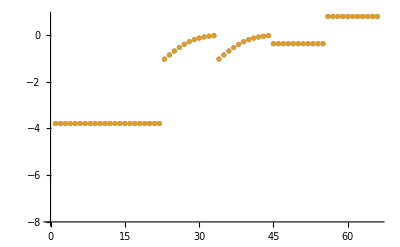

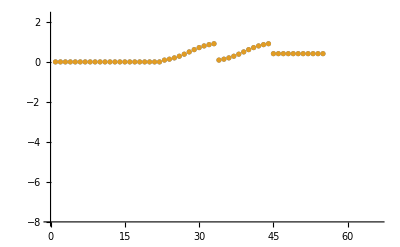

```mathematica
datasetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet =63;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

{1,1}

{fdp^c→∞}

fdp^c

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{fdp^c→(0.00742751 (4.52597×10^29+1.02536×10^32 cit^c))/(1.67872×10^32+4.70406×10^29 cit^c)}}

{1,1}

{fdp^c→∞}

fdp^c

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{fdp^c→0.0000699269}}

data value | predicted value | error in %
0.00002 | 0.0000200252 | 0.126211
0.00007 | 0.0000699269 | 0.104479

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
0.217 | 0.159464 | 26.5143
3.17 | 2.1908 | 30.8897

```mathematica
backCalculateRatios[haldaneRatiosList, {KeqList[[1]][[3]],KeqList[[1]][[3]]}, paramFitSub]//TableForm
```

data value | predicted value | error in %
0.00016
0.00016 | 0.000336501
0.00022521 | 110.313
40.756

#### Export rate back calculated parameter error distribution

```mathematica
Get["MASSef`"]
```

```mathematica
kmList
```

{{5,fdp,0.00002,{0.000018,0.000022},{},M,8,30,{{trishcl,0.05}},{}},{5,fdp,0.00007,{0.000058,0.000082},{{cit,0.011}},M,8,30,{{trishcl,0.05}},{}}}

```mathematica
Get["MASSef`"]
```

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
nRateSets=1200;
predictedParamsErrorList=Table[

paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];
{filteredDataList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2;;,3]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2;;,3]],
backCalculateRatios[haldaneRatiosList, {KeqList[[1]][[3]],KeqList[[1]][[3]]},  paramFitSub][[2;;,3]]}//Flatten,
{rateSetI, 1, nRateSets}];

predictedParamsErrorList=Insert[predictedParamsErrorList,{"ssd","Km","Km_cit","kcat", "kcat_cit","Keq", "Keq_cit"} , 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{0,kmList[[1]][[3]],kmList[[2]][[3]],kcatList[[1]][[3]],kcatList[[2]][[3]], KeqList[[1]][[3]],  KeqList[[1]][[3]]}  ,2];;
Export[outputPath<>"/treated_data/predicted_params_error_distribution_p10.csv",predictedParamsErrorList,"CSV"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

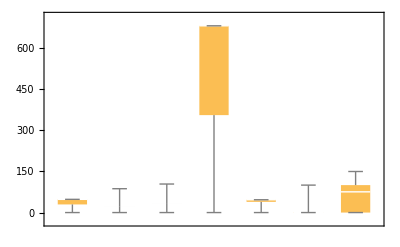

```mathematica
BoxWhiskerChart[Transpose@predictedParamsErrorList[[3;;50,All]]]
```

```mathematica
outputPath<>"/treated_data/predicted_params_error_distribution.csv"
```

/home/mrama/Dropbox/MASSef/examples/FBA1/fit_FBA1/output/treated_data/predicted_params_error_distribution.csv

#### Export rate back calculated parameter distribution

```mathematica
nRateSets=100;
predictedParamsList=Table[

paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];
{filteredDataList[[rateSetI,1]],
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName][[2;;,2]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2;;,2]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,2]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsList=Insert[predictedParamsList,{"ssd","Km_fdp1","Km_fdp2","kcat_f1", "kcat_f2","Keq"} , 1];
predictedParamsList=Insert[predictedParamsList,{"Null",kmList[[1]][[3]],kmList[[2]][[3]],kcatList[[1]][[3]],kcatList[[2]][[3]], KeqList[[1]][[3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_distribution.csv",predictedParamsList,"CSV"];
```